```mathematica
(* Calculate parameter spaces for various szenarios *)
ClearAll	
Clear[Nc,Nd,nfc,nsc,nfd,nsd,nfj,nsj,Nfc,Nfd,Nsc,Nsd,X1,X2,Y1,Y2,Z1,Z2,coeff]
(* Initialize variables ->*)
	Get["Documents/QCDxdQCD/Mathematica/Packages/Beta'.m"]
	norm = {1/(4*Pi), 1/(4*Pi)};
	model = {Nc,Nd,nfc,nsc,nfd,nsd,nfj,nsj};
	coeff	= (c@@Join[norm,model])/.{
		nfc -> Nfc-Nd*nfj ,
		nsc -> Nsc-Nd*nsj ,
		nfd -> Nfd-Nc*nfj ,
		nsd -> Nsd-Nc*nsj 
	};
	(*reduced model*)

	X1 = coeff[[1]]; 
	Y1 = coeff[[2]]; 
	Z1 = coeff[[3]]; 
	X2 = coeff[[4]]; 
	Y2 = coeff[[5]]; 
	Z2 = coeff[[6]];
	 
	det   = Y1*Y2 - Z1*Z2;
	afix2 = {(-X2/Y2) , 0 };
	afix3 = {0 , (-X1/Y1)};
	afix4 = {(Z1*X2-X1*Y2)/(det),
		     (Z2*X1-X2*Y1)/(det)
	};
	
(*<-Initialize variables *)
```

ClearAll

```mathematica
(* General conditions *)
(* f0:all particle numbers physical *)
f0=(Nc≥1&&Nd≥1&&Nfc≥Nd*nfj&&Nsc≥Nd*nsj&&Nfd≥Nc*nfj&&Nsd≥Nc*nsj&&nfj≥0&&nsj≥0
);
(* f1:all particle numbers integer *)
f1 = (Element[Nc,Integers] 
&& Element[Nd,Integers]
&& Element[Nfc,Integers]
&& Element[Nsc,Integers]
&& Element[Nfd,Integers]
&& Element[Nsd,Integers]
&& Element[nfj,Integers]
&& Element[nsj,Integers]
);
(*f2:afix2 is physical*)
f2=afix2[[1]]≥0&&afix2[[2]]≥0;
(*f3:afix3 is physical*)
f3=afix3[[1]]≥0&&afix3[[2]]≥0;
(*f4:afix4 is physical*)
f4=afix4[[1]]≥0&&afix4[[2]]≥0;
(*f2a:afix2 is UV in alpha_1-direction*)
f2a=X1-Z1*X2/Y2<0;
(*f2b:afix2 is UV in alpha_2-direction*)
f2b=(afix2[[1]]^2*Y1+afix2[[2]]^2*Y2<0);
(*f3a:afix3 is UV in alpha_1-direction*)
f3a=(afix3[[1]]^2*Y1+afix3[[2]]^2*Y2<0);
(*f3b:afix3 is UV in alpha_2-direction*)
f3b=X2-Z2*X1/Y1<0;
(*f4a:afix4 is UV-attractive*)
f4a=(afix4[[1]]^2*Y1+afix4[[2]]^2*Y2<0&&afix4[[1]]^2*afix4[[2]]^2*det>0);
(*f4b:afix4 is UV-repulsive*)
f4b=(afix4[[1]]^2*Y1+afix4[[2]]^2*Y2>0&&afix4[[1]]^2*afix4[[2]]^2*det>0);
(*f4c:afix4 is saddlepoint*)
f4c=afix4[[1]]^2*afix4[[2]]^2*det<0;
```

```mathematica
(*---------*)
(* A FIX 3 *)
(*---------*)
Clear[a,Nc,Nd,Nfc,Nfd,Nsc,nfj,nsj,nfc,nfd,nsc,nsd,c1,c2,c3,c4,x]
c4={Nfc->nfc+Nd*nfj, Nfd->nfd+Nc*nfj,Nsc->nsc+Nd*nsj, Nsd->nsd +Nc*nsj};
c1=(X1<0 &&Y1>0)/.c4;
c2 = (X2*Y1<Z2*X1)/.c4;
noscalar=(nsc==0&&nsd==0&&nsj==0);


a=(-X1/Y1)/.c4;
a/.{Nc->3, Nd->9,nfc->6, nsc->0, nfd->60,nsd->0,nfj->1,nsj->0};
N[%]
```

0.1428

```mathematica
(*-----------------------*)
(* afix3 without scalars *)
(*-----------------------*)
Do[
Print[StringJoin["nfc=",ToString[k]]]
Do[
Do[
Clear[x];
x=Reduce[noscalar&&c1&&c2&&Nc==3&&nfc==k && Nd==i && nfd== j&&Element[nfj,Integers]];
If[ToString[x]≠ToString[False],Print[x] ];
,{j,40,56}
];
,{i,9,9}
],{k,6,6}
]
```

nfc=6

nfj==1&&nsj==0&&nsd==0&&nsc==0&&nfd==40&&nfc==6&&Nd==9&&Nc==3

nfj==1&&nsj==0&&nsd==0&&nsc==0&&nfd==41&&nfc==6&&Nd==9&&Nc==3

nfj==1&&nsj==0&&nsd==0&&nsc==0&&nfd==42&&nfc==6&&Nd==9&&Nc==3

nfj==1&&nsj==0&&nsd==0&&nsc==0&&nfd==43&&nfc==6&&Nd==9&&Nc==3

nfj==1&&nsj==0&&nsd==0&&nsc==0&&nfd==44&&nfc==6&&Nd==9&&Nc==3

nfj==1&&nsj==0&&nsd==0&&nsc==0&&nfd==45&&nfc==6&&Nd==9&&Nc==3

nfj==1&&nsj==0&&nsd==0&&nsc==0&&nfd==46&&nfc==6&&Nd==9&&Nc==3

```mathematica
(*-----------------------*)
(*afix3 including scalars*)
(*-----------------------*)
Do[
Print[StringJoin["nfc=",ToString[k]]]
Do[
Do[
Clear[x];
x=Reduce[nfj==0&&nfd==0&&c1&&c2&&Nc==3&&nfc==k &&nsc==0&& Nd==i && nsd== j&&Element[nsj,Integers]];
If[ToString[x]≠ToString[False],Print[x] ];
,{j,0,10}
];
,{i,2,3}
],{k,6,6}
]
```

nfc=6

(nsj==4||nsj==5||nsj==6||nsj==7||nsj==8||nsj==9||nsj==10||nsj==11||nsj==12||nsj==13)&&nsd==0&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==3&&Nc==3

(nsj==5||nsj==6||nsj==7||nsj==8||nsj==9||nsj==10||nsj==11||nsj==12||nsj==13)&&nsd==1&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==3&&Nc==3

(nsj==5||nsj==6||nsj==7||nsj==8||nsj==9||nsj==10||nsj==11||nsj==12||nsj==13)&&nsd==2&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==3&&Nc==3

(nsj==5||nsj==6||nsj==7||nsj==8||nsj==9||nsj==10||nsj==11||nsj==12||nsj==13)&&nsd==3&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==3&&Nc==3

(nsj==5||nsj==6||nsj==7||nsj==8||nsj==9||nsj==10||nsj==11||nsj==12||nsj==13)&&nsd==4&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==3&&Nc==3

(nsj==5||nsj==6||nsj==7||nsj==8||nsj==9||nsj==10||nsj==11||nsj==12||nsj==13)&&nsd==5&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==3&&Nc==3

(nsj==5||nsj==6||nsj==7||nsj==8||nsj==9||nsj==10||nsj==11||nsj==12||nsj==13)&&nsd==6&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==3&&Nc==3

(nsj==5||nsj==6||nsj==7||nsj==8||nsj==9||nsj==10||nsj==11||nsj==12||nsj==13)&&nsd==7&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==3&&Nc==3

(nsj==5||nsj==6||nsj==7||nsj==8||nsj==9||nsj==10||nsj==11||nsj==12||nsj==13)&&nsd==8&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==3&&Nc==3

(nsj==5||nsj==6||nsj==7||nsj==8||nsj==9||nsj==10||nsj==11||nsj==12||nsj==13)&&nsd==9&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==3&&Nc==3

(nsj==5||nsj==6||nsj==7||nsj==8||nsj==9||nsj==10||nsj==11||nsj==12||nsj==13)&&nsd==10&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==3&&Nc==3

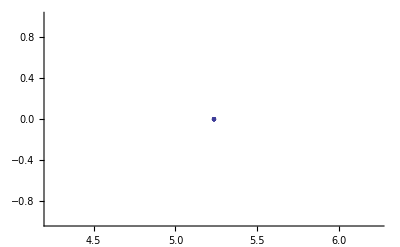

```mathematica
(* SCATTER PLOT afix3 *)
Clear[a,x1,x2,y1,y2,z1,z2,f,c1,c2,c3,c4,f1,f2];
Clear[Nc,Nd,Nfc,Nfd,Nsc,Nsd,nfj,nsj];

x1=X1/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};
y1=Y1/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};
z1=Z1/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};
x2=X2/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};
y2=Y2/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};
z2=Z2/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};

a={-x1/y1,0};

Clear[list1,list2,list,c1]
c1 = {Nc->3, Nd->3, nfc->6, nsc->0,nsd->0,nfj->1,nsj->0};
a=a/.c1;

list=List[];

Do[
If[(a/.{nfd->i})[[1]]>0,
list=Append[list,a/.{nfd->i}];
]

,{i,1,10}
];


 Needs["PlotLegends`"]
ListPlot[list,PlotLegend->{"afix 3"},LegendPosition->{0.3,-0.7}]
```

```mathematica
(*---------*)
(* A FIX 4 *)
(*---------*)
(*-----------------------*)
(* attractive fixed point*)
(*-----------------------*)
Clear[Nc,Nd,Nfc,Nfd,Nsc,nfj,nsj,nfc,nfd,c1,c2,c3,c4,x]
noskalar = (Nsc==0 && Nsd ==0 && nsj ==0);
sm = (Nc==3 && nfc==6);

(*-----------------------*)
(*       without scalars *)
(*-----------------------*)
Clear[c1,c2,c3,c4]
c1 =FullSimplify[ (X1>0&&Y1<0)/.{Nsc->0, Nsd->0, nsj->0}]

Do[
Print[StringJoin["nfc=",ToString[k]]]
Do[
Do[
Clear[x];
x=Reduce[c1&&c2&&c3&&Nc==3&&nfc==k && Nd==i && nfd== j&&Element[nfj,Integers]];
If[ToString[x]≠ToString[False],Print[x] ];
,{j,0,50}
];
,{i,1,50}
],{k,5,10}
]
```

False

```mathematica
(*-----------------------*)
(*     including scalars *)
(*-----------------------*)
Clear[c1,c2,c3,c4]
c1 =FullSimplify[ (f0&&X1>0&&Y1<0)];

c2=FullSimplify[Reduce[c1 &&f1,Nsc]];

c3=FullSimplify[Reduce[c2&&afix4[[1]]>0&&afix4[[2]]>0] ]
```

Nc≥1&&Nd≥1&&Nfc≥Nd nfj&&Nsc≥Nd nsj&&Nfd≥Nc nfj&&Nsd≥Nc nsj&&nfj≥0&&nsj≥0&&4 Nfc+Nsc>22 Nc&&Nc^3 (13 Nfc+4 Nsc)<34 Nc^4+3 Nc (Nfc+Nsc)

Nc==1&&((Nfd≥0&&nfj==0&&((Nd≥1&&Nsd≥0&&nsj==0&&((Nfc==0&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nfc==1&&(Nsc==19||Nsc==20||Nsc==21||Nsc==22||Nsc==23)))&&(Nd|Nfd|Nsd)∈Integers)||(((Nsd≥1&&nsj==1&&((Nfc==0&&(((Nd==1||Nd==2||Nd==3||Nd==4||Nd==5||Nd==6||Nd==7||Nd==8||Nd==9||Nd==10||Nd==11||Nd==12||Nd==13||Nd==14||Nd==15||Nd==16||Nd==17||Nd==18||Nd==19||Nd==20||Nd==21||Nd==22||Nd==23)&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==24&&(Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==25&&(Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==26&&(Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==27&&(Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==28&&(Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==29&&(Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==30&&(Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==31&&(Nsc==31||Nsc==32||Nsc==33))||(Nd==32&&(Nsc==32||Nsc==33))||(Nsc==33&&Nd==33)))||(Nfc==1&&((Nsc==23&&(Nd==1||Nd==2||Nd==3||Nd==4||Nd==5||Nd==6||Nd==7||Nd==8||Nd==9||Nd==10||Nd==11||Nd==12||Nd==13||Nd==14||Nd==15||Nd==16||Nd==17||Nd==18||Nd==19||Nd==20||Nd==21||Nd==22||Nd==23))||((Nd==1||Nd==2||Nd==3||Nd==4||Nd==5||Nd==6||Nd==7||Nd==8||Nd==9||Nd==10||Nd==11||Nd==12||Nd==13||Nd==14||Nd==15||Nd==16||Nd==17||Nd==18||Nd==19)&&(Nsc==19||Nsc==20||Nsc==21||Nsc==22))||(Nd==20&&(Nsc==20||Nsc==21||Nsc==22))||(Nd==21&&(Nsc==21||Nsc==22))||(Nd==22&&Nsc==22)))))||(Nsd≥2&&nsj==2&&((Nfc==0&&((Nsc==23&&(Nd==1||Nd==2||Nd==3||Nd==4||Nd==5||Nd==6||Nd==7||Nd==8||Nd==9||Nd==10||Nd==11))||((Nd==1||Nd==2||Nd==3||Nd==4||Nd==5||Nd==6||Nd==7||Nd==8||Nd==9||Nd==10||Nd==11||Nd==12)&&(Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==13&&(Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==14&&(Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==15&&(Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==16&&(Nsc==32||Nsc==33))))||(Nfc==1&&(((Nsc==19||Nsc==20||Nsc==21||Nsc==22||Nsc==23)&&(Nd==1||Nd==2||Nd==3||Nd==4||Nd==5||Nd==6||Nd==7||Nd==8||Nd==9))||(Nd==10&&(Nsc==20||Nsc==21||Nsc==22||Nsc==23))||(Nd==11&&(Nsc==22||Nsc==23))))))||(Nsd≥3&&nsj==3&&((Nfc==0&&((Nsc==23&&(Nd==1||Nd==2||Nd==3||Nd==4||Nd==5||Nd==6||Nd==7))||((Nd==1||Nd==2||Nd==3||Nd==4||Nd==5||Nd==6||Nd==7||Nd==8)&&(Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==9&&(Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==10&&(Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==11&&Nsc==33)))||(Nfc==1&&(((Nsc==19||Nsc==20||Nsc==21||Nsc==22||Nsc==23)&&(Nd==1||Nd==2||Nd==3||Nd==4||Nd==5||Nd==6))||(Nd==7&&(Nsc==21||Nsc==22||Nsc==23))))))||(Nsd≥4&&nsj==4&&((Nfc==0&&((Nsc==23&&(Nd==1||Nd==2||Nd==3||Nd==4||Nd==5))||((Nd==1||Nd==2||Nd==3||Nd==4||Nd==5||Nd==6)&&(Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==7&&(Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==8&&(Nsc==32||Nsc==33))))||(Nfc==1&&(((Nsc==19||Nsc==20||Nsc==21||Nsc==22||Nsc==23)&&(Nd==1||Nd==2||Nd==3||Nd==4))||(Nd==5&&(Nsc==20||Nsc==21||Nsc==22||Nsc==23))))))||(Nsd≥5&&nsj==5&&((Nfc==0&&(((Nd==1||Nd==2||Nd==3||Nd==4)&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==5&&(Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==6&&(Nsc==30||Nsc==31||Nsc==32||Nsc==33))))||(Nfc==1&&(((Nsc==19||Nsc==20||Nsc==21||Nsc==22||Nsc==23)&&(Nd==1||Nd==2||Nd==3))||(Nd==4&&(Nsc==20||Nsc==21||Nsc==22||Nsc==23))))))||(Nsd≥6&&nsj==6&&((Nfc==0&&((Nsc==23&&(Nd==1||Nd==2||Nd==3))||((Nd==1||Nd==2||Nd==3||Nd==4)&&(Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==5&&(Nsc==30||Nsc==31||Nsc==32||Nsc==33))))||(Nfc==1&&(Nd==1||Nd==2||Nd==3)&&(Nsc==23||Nsc==19||Nsc==20||Nsc==21||Nsc==22))))||(Nsd≥7&&nsj==7&&((Nfc==0&&(((Nd==1||Nd==2||Nd==3)&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==4&&(Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))))||(Nfc==1&&(((Nsc==19||Nsc==20||Nsc==21||Nsc==22||Nsc==23)&&(Nd==1||Nd==2))||(Nd==3&&(Nsc==21||Nsc==22||Nsc==23))))))||(Nsd≥8&&nsj==8&&((Nfc==0&&((Nsc==23&&(Nd==1||Nd==2))||((Nd==1||Nd==2||Nd==3)&&(Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==4&&(Nsc==32||Nsc==33))))||(Nfc==1&&(Nd==1||Nd==2)&&(Nsc==23||Nsc==19||Nsc==20||Nsc==21||Nsc==22))))||(Nsd≥9&&nsj==9&&((((Nfc==0&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nfc==1&&(Nsc==19||Nsc==20||Nsc==21||Nsc==22||Nsc==23)))&&(Nd==1||Nd==2))||(Nd==3&&Nfc==0&&(Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))))||(Nsd≥10&&nsj==10&&((Nfc==0&&(((Nd==1||Nd==2)&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==3&&(Nsc==30||Nsc==31||Nsc==32||Nsc==33))))||(Nfc==1&&((Nd==1&&(Nsc==19||Nsc==20||Nsc==21||Nsc==22||Nsc==23))||(Nd==2&&(Nsc==20||Nsc==21||Nsc==22||Nsc==23))))))||(Nsd≥11&&nsj==11&&((Nfc==0&&(((Nd==1||Nd==2)&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==3&&Nsc==33)))||(Nfc==1&&((Nd==1&&(Nsc==19||Nsc==20||Nsc==21||Nsc==22||Nsc==23))||(Nd==2&&(Nsc==22||Nsc==23))))))||(Nsd≥12&&nsj==12&&((Nfc==0&&((Nd==1&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==2&&(Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))))||(Nd==1&&Nfc==1&&(Nsc==19||Nsc==20||Nsc==21||Nsc==22||Nsc==23))))||(Nsd≥13&&nsj==13&&((Nfc==0&&((Nd==1&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==2&&(Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))))||(Nd==1&&Nfc==1&&(Nsc==19||Nsc==20||Nsc==21||Nsc==22||Nsc==23))))||(Nsd≥14&&nsj==14&&((Nfc==0&&((Nd==1&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==2&&(Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))))||(Nd==1&&Nfc==1&&(Nsc==19||Nsc==20||Nsc==21||Nsc==22||Nsc==23))))||(Nsd≥15&&nsj==15&&((Nfc==0&&((Nd==1&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==2&&(Nsc==30||Nsc==31||Nsc==32||Nsc==33))))||(Nd==1&&Nfc==1&&(Nsc==19||Nsc==20||Nsc==21||Nsc==22||Nsc==23))))||(Nsd≥16&&nsj==16&&((Nfc==0&&((Nd==1&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nd==2&&(Nsc==32||Nsc==33))))||(Nd==1&&Nfc==1&&(Nsc==19||Nsc==20||Nsc==21||Nsc==22||Nsc==23))))||(Nd==1&&((((Nfc==0&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nfc==1&&(Nsc==19||Nsc==20||Nsc==21||Nsc==22||Nsc==23)))&&((nsj==17&&Nsd≥17)||(Nsd≥18&&nsj==18)||(Nsd≥19&&nsj==19)))||(Nsd≥20&&nsj==20&&((Nfc==0&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nfc==1&&(Nsc==20||Nsc==21||Nsc==22||Nsc==23))))||(Nsd≥21&&nsj==21&&((Nfc==0&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nfc==1&&(Nsc==21||Nsc==22||Nsc==23))))||(Nsd≥22&&nsj==22&&((Nfc==0&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nfc==1&&(Nsc==22||Nsc==23))))||(Nsd≥23&&nsj==23&&((Nfc==0&&(Nsc==23||Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nfc==1&&Nsc==23)))||(Nfc==0&&((Nsd≥24&&nsj==24&&(Nsc==24||Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nsd≥25&&nsj==25&&(Nsc==25||Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nsd≥26&&nsj==26&&(Nsc==26||Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nsd≥27&&nsj==27&&(Nsc==27||Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nsd≥28&&nsj==28&&(Nsc==28||Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nsd≥29&&nsj==29&&(Nsc==29||Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nsd≥30&&nsj==30&&(Nsc==30||Nsc==31||Nsc==32||Nsc==33))||(Nsd≥31&&nsj==31&&(Nsc==31||Nsc==32||Nsc==33))||(Nsd≥32&&nsj==32&&(Nsc==32||Nsc==33))||(Nsc==33&&Nsd≥33&&nsj==33))))))&&(Nfd|Nsd)∈Integers)))||(Nd==1&&Nfc==1&&Nfd≥1&&nfj==1&&(((Nsc==19||Nsc==20||Nsc==21||Nsc==22||Nsc==23)&&((Nsd≥0&&nsj==0)||(Nsd≥1&&nsj==1)||(Nsd≥2&&nsj==2)||(Nsd≥3&&nsj==3)||(Nsd≥4&&nsj==4)||(Nsd≥5&&nsj==5)||(Nsd≥6&&nsj==6)||(Nsd≥7&&nsj==7)||(Nsd≥8&&nsj==8)||(Nsd≥9&&nsj==9)||(Nsd≥10&&nsj==10)||(Nsd≥11&&nsj==11)||(Nsd≥12&&nsj==12)||(Nsd≥13&&nsj==13)||(Nsd≥14&&nsj==14)||(Nsd≥15&&nsj==15)||(Nsd≥16&&nsj==16)||(Nsd≥17&&nsj==17)||(Nsd≥18&&nsj==18)||(Nsd≥19&&nsj==19)))||(Nsd≥20&&nsj==20&&(Nsc==20||Nsc==21||Nsc==22||Nsc==23))||(Nsd≥21&&nsj==21&&(Nsc==21||Nsc==22||Nsc==23))||(Nsd≥22&&nsj==22&&(Nsc==22||Nsc==23))||(Nsc==23&&Nsd≥23&&nsj==23))&&(Nfd|Nsd)∈Integers))

```mathematica
(*-----------------------*)
(* saddlepoint           *)
(*-----------------------*)

Clear[Nc,Nd,Nfc,Nfd,Nsc,nfj,nsj,nfc,nfd,c1,c2,c3,c4,x]
(*-----------------------*)
(*       without scalars *)
(*-----------------------*)
noskalar = (Nsc==0 && Nsd ==0 && nsj ==0);
sm = (Nc==3 && nfc==6);

c1 =FullSimplify[( Z1*Z2 >  Y1*Y2  )/.{Nsc->0, Nsd->0, nsj->0}] ;
c2 =FullSimplify[( Z1*X2 <  X1*Y2  )/.{Nsc->0, Nsd->0, nsj->0}] ;
c3 =FullSimplify[( Z2*X1 <  X2*Y1  )/.{Nsc->0, Nsd->0, nsj->0}] ;




c4={Nfc->nfc+Nd*nfj, Nfd->nfd+Nc*nfj};
c1=c1/.c4;
c2=c2/.c4; 
c3=c3/.c4;

Do[
Print[StringJoin["nfc=",ToString[k]]]
Do[
Do[
Clear[x];
x=Reduce[c1&&c2&&c3&&Nc==3&&nfc==k && Nd==i && nfd== j&&Element[nfj,Integers]];
If[ToString[x]≠ToString[False],Print[x] ];
,{j,0,50}
];
,{i,1,50}
],{k,5,10}
]
```

nfc=5

nfj==2&&nfd==0&&nfc==5&&Nd==2&&Nc==3

nfj==1&&nfd==0&&nfc==5&&Nd==3&&Nc==3

nfj==1&&nfd==1&&nfc==5&&Nd==3&&Nc==3

nfj==1&&nfd==2&&nfc==5&&Nd==3&&Nc==3

nfj==1&&nfd==3&&nfc==5&&Nd==3&&Nc==3

nfj==1&&nfd==4&&nfc==5&&Nd==3&&Nc==3

nfj==1&&nfd==5&&nfc==5&&Nd==3&&Nc==3

nfc=6

nfj==1&&nfd==0&&nfc==6&&Nd==2&&Nc==3

nfj==1&&nfd==1&&nfc==6&&Nd==2&&Nc==3

nfj==1&&nfd==2&&nfc==6&&Nd==2&&Nc==3

nfc=7

nfc=8

nfj==1&&nfd==0&&nfc==8&&Nd==1&&Nc==3

nfc=9

nfc=10

```mathematica
(*-----------------------*)
(* including scalars     *)
(*-----------------------*)
Clear[c1,c2,c3,c4]
c1 =FullSimplify[( Z1*Z2 >  Y1*Y2  )];
c2 =FullSimplify[( Z1*X2 <  X1*Y2  )];
c3 =FullSimplify[( Z2*X1 <  X2*Y1  )];




c4={Nfc->nfc+Nd*nfj, Nfd->nfd+Nc*nfj,Nsc->nsc+Nd*nsj, Nsd->nsd +Nc*nsj};
c1=c1/.c4;
c2=c2/.c4; 
c3=c3/.c4;


Do[
Print[StringJoin["nfc=",ToString[k]]]
Do[
Do[
Clear[x];
x=FullSimplify[Reduce[c1&&c2&&c3&&Nc==3&&nfc==k && 
nsc==0&&Nd==i && nfd== 0&&nsd==j&&nfj==0&&Element[nsj,Integers]]
];
If[ToString[x]≠ToString[False],Print[x] ];
,{j,0,100}
];
,{i,6,6}
],{k,6,6}
]
```

nfc=6

nsj==1&&nsd==41&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

nsj==1&&nsd==42&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

nsj==1&&nsd==43&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

nsj==1&&nsd==44&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

nsj==1&&nsd==45&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

nsj==1&&nsd==46&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

nsj==1&&nsd==47&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

nsj==1&&nsd==48&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

nsj==1&&nsd==49&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

nsj==1&&nsd==50&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

nsj==1&&nsd==51&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

nsj==1&&nsd==52&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

nsj==1&&nsd==53&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

nsj==1&&nsd==54&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

nsj==1&&nsd==55&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

nsj==1&&nsd==56&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

nsj==1&&nsd==57&&nsc==0&&nfj==0&&nfd==0&&nfc==6&&Nd==6&&Nc==3

```mathematica
Clear[x1,x2,y1,y2,z1,z2,f,c1,c2,c3,c4,f1,f2];
Clear[Nc,Nd,Nfc,Nfd,Nsc,Nsd,nfj,nsj];

x1=X1/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};
y1=Y1/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};
z1=Z1/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};
x2=X2/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};
y2=Y2/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};
z2=Z2/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};
Clear[a]
a=FullSimplify[{(z1*x2-x1*y2)/(y1*y2-z1*z2), (z2*x1-x2*y1)/(y1*y2-z1*z2)}
];
(*
N[a/.{Nc->3,Nd->2,nfc->6,nfd->1,nsj->0,nsc->0,nfd->1,nfj->1,nsd->0}]
*)
Do[
Print[N[
a/.{Nc->3,Nd->2,nfc->6,nsc->0,nfd->0,nsd->i,nsj->9,nfj->0}
]]
,{i,0,5}
]
```

{0.211311,1.54863}

{0.100732,1.71245}

{-0.025254,1.8991}

{-0.170109,2.1137}

{-0.338416,2.36304}

{-0.536369,2.65631}

```mathematica
Clear[n]
n[x_,y_]:=Sqrt[ 34/(13-3/y^2)* 34/(13-3/x^2)]

N[n[2,2]]
```

2.77551

```mathematica
Clear[n1,n2,g1,g2,nc,n,nd,nfc,nfd,nmin,napprox,x,y]
g1[x_,y_]:=2/3 x -11/3y
g2[x_,y_]:=(13/3 x - 1/x)y -34/3 x^2
n1[nc_,nd_,nfc_,nfd_]:=g1[nfd,nd]/g1[nfc,nc] * g2[nc,nfc]/(nc^2-1)
n2[nc_,nd_,nfc_,nfd_]:=n1[nd,nc,nfd,nfc]

nmin[nc_,nd_,nfc_,nfd_]:= g2[nc,nfc]*g2[nd,nfd]/((nc^2-1)*(nd^2-1))
napprox[x_,y_]:=((13/3y-1/y)34 y/(13-3/y) -34/3y^2)((13/3x-1/x)34 x/(13-3/x) -34/3 x^2)/((x^2-1)*(y^2-1))

N[nmin[3,3,6+3*3,3*3]]
```

16.5

{1/(2 π),63/(4 π^2),3/(8 π^2),2/(3 π),365/(48 π^2),1/π^2}

{-(682 π)/22923,-(640 π)/7641}

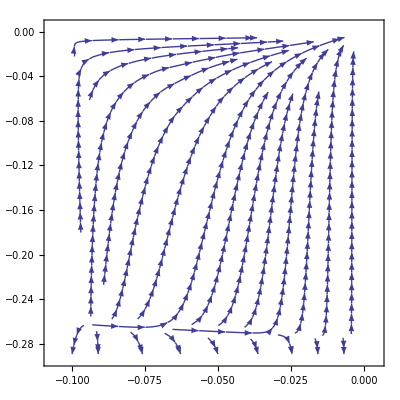

```mathematica
(* PLOT *)
Clear[Nc,Nd,Nfc,Nsc,Nfd,Nsd,nfj,nsj]
Nc=3;
Nd =2;
Nfc =18;
Nsc=0;
Nfd=13;
Nsd = 0;
nfj =1;
nsj=0;

coeff
afix4


Clear[f,f1,f2,x,y]
f1[x_,y_]:=X1 x^2 +Y1 x^3 + Z1 x^2 *y
f2[x_,y_]:=X2 y^2 +Y2 y^3 + Z2 y^2 *x




StreamPlot[{f1[x,y],f2[x,y]},{x,0,afix4[[1]]*1.1},{y,0,afix4[[2]]*1.1}]
```

{(2 (378 nsj-570 Nd^2 nsj+32 Nd^4 nsj+3 Nd^3 (476+nsj^2)) π)/(-702 nsj+936 Nd^2 nsj+374 Nd^4 nsj+27 Nd nsj^2-12 Nd^3 (221+5 nsj^2)),(2 Nd (774 nsj+Nd (1716-242 Nd nsj+9 nsj^2)) π)/(-702 nsj+936 Nd^2 nsj+374 Nd^4 nsj+27 Nd nsj^2-12 Nd^3 (221+5 nsj^2))}

{-(2 (1204+9 (-20+nsj) nsj) π)/(2236+nsj (-1804+171 nsj)),-(2 (1196+nsj (-248+9 nsj)) π)/(2236+nsj (-1804+171 nsj))}

{-10.7637,-9.97182}

{8.03663,6.72155}

{2.85948,2.04578}

{1.7584,0.974398}

{1.32475,0.453271}

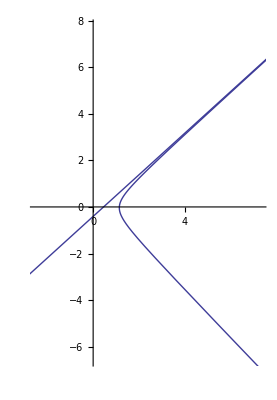

```mathematica
(* SCATTER PLOT afix4*)
Clear[a,x1,x2,y1,y2,z1,z2,f,c1,c2,c3,c4,f1,f2];
Clear[Nc,Nd,Nfc,Nfd,Nsc,Nsd,nfj,nsj];

x1=X1/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};
y1=Y1/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};
z1=Z1/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};
x2=X2/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};
y2=Y2/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};
z2=Z2/.{Nsc->nsc+Nd*nsj,Nsd->nsd+Nc*nsj,Nfc->nfc+Nd*nfj,Nfd->nfd+Nc*nfj};

FullSimplify[{(z1*x2-x1*y2)/(y1*y2-z1*z2), (z2*x1-x2*y1)/(y1*y2-z1*z2)}/.{Nc->3, nfc->6, nsc->0,nfd->0,nfj->0,nsd->0}]

a[x_]:=FullSimplify[({(z1*x2-x1*y2)/(y1*y2-z1*z2), (z2*x1-x2*y1)/(y1*y2-z1*z2)})/.{Nc->3, Nd->3, nfc->6, nsc->0,nfd->0,nsd->20,nfj->0,nsj->x}
];
FullSimplify[a[nsj]]
N[a[1]]
N[a[2]]
N[a[3]]
N[a[4]]
N[a[5]]
ParametricPlot[{a[x][[1]],a[x][[2]]},{x,1,9}]
```

```mathematica
Clear[list1,list2,list,c1]
c1 = {Nc->3, Nd->2, nfc->6, nsc->0,nfd->0,nfj->0};
a=a/.c1;

list=List[];

Do[
Clear[list1];
list1=List[];
Do[
If[(a/.{nsj->i,nsd->j})[[1]]>0&&(a/.{nsj->i,nsd->j})[[2]]>0,
list1=Append[list1,a/.{nsj->i,nsd->j}];
]

,{i,1,8}
];
list=Append[list,list1];
,{j,1,5}
]
```

Part::partd: Part specification a ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification a ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification a ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

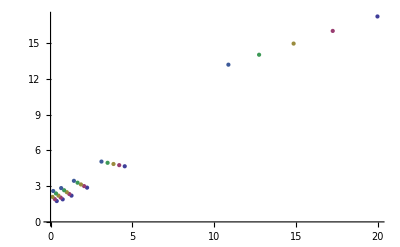

```mathematica
Needs["PlotLegends`"]
ListPlot[list,PlotLegend->{"1","2","3","4","5"},LegendPosition->{0.3,-0.4}]
```

```mathematica
(*---------*)
(* A FIX 2 *)
(*---------*)
Clear[a,Nc,Nd,Nfc,Nfd,Nsc,nfj,nsj,nfc,nfd,nsc,nsd,c1,c2,c3,c4,x]
c4={Nfc->nfc+Nd*nfj, Nfd->nfd+Nc*nfj,Nsc->nsc+Nd*nsj, Nsd->nsd +Nc*nsj};
c1=(X2<0 &&Y2>0)/.c4;
c2 = (X1*Y2<Z1*X2)/.c4;
noscalar=(nsc==0&&nsd==0&&nsj==0&&nfj≥1);


a=(-X2/Y2)/.c4;
a/.{Nc->3, Nd->2,nfc->6, nsc->0, nfd->5,nsd->0,nfj->2,nsj->0};
N[%]
```

0.

```mathematica
(*-----------------------*)
(* afix2 without scalars *)
(*-----------------------*)
Do[
Print[StringJoin["nfc=",ToString[k]]]
Do[
Do[
Clear[x];
x=Reduce[noscalar&&c1&&c2&&Nc==3&&nfc==k && Nd==i && nfd== j&&Element[nfj,Integers]];
If[ToString[x]≠ToString[False],Print[x] ];
,{j,0,100}
];
,{i,11,11}
],{k,6,6}
]
```

nfc=6